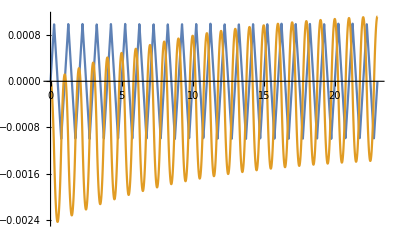

```mathematica
LVal=0.01;
CVal=0.1;
RVal=100; 
TMax=23;
Eq =  TriangleWave[t]+LVal q''[t] + q[t]/CVal + q'[t] RVal ==0 ;
qSol=NDSolveValue[ {Eq, q[0]==0,q'[0]==0},q, {t, 0, TMax}];
Plot[{0.001TriangleWave[t],qSol[t]},{t, 0, TMax}]
```

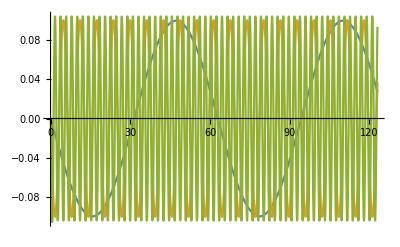

```mathematica
Clear[ω,Eq,qSol]
LVal=0.1;
CVal=0.1;
RVal=1; 
TMax=123;
Eq[ω_] =  Sin[ω t]+LVal q''[t] + q[t]/CVal + q'[t] RVal ==0 ;
qSol[.1]=NDSolveValue[ {Eq[.1], q[0]==0,q'[0]==0},q, {t, 0, TMax}];
qSol[1]=NDSolveValue[ {Eq[1], q[0]==0,q'[0]==0},q, {t, 0, TMax}];
qSol[3]=NDSolveValue[ {Eq[3], q[0]==0,q'[0]==0},q, {t, 0, TMax}];
Plot[{qSol[0.1][t],qSol[1][t],qSol[3][t]},{t, 0, TMax}]
```

```mathematica
?SawtoothWave
```